```mathematica
FFT[invec_]:= Module[{ elist, olist, netlist, eft, oft, n, omega},
If[Length[invec]== 1, (*shamelessly ripped out of joel's fft chapter, identical except for my aesthetic preference for Do over For*)
Return[invec];];
n= Length[invec];
omega = 1;
elist = Table[invec[[j]], {j, 1, n, 2}];
olist=  Table[invec[[j]], {j, 2, n, 2}];
eft =FFT[elist];
oft = FFT[olist];
netlist = Table[0,{j, 0, n -1}];
For[k= 0,k ≤  n/2-1, k = k + 1,
netlist[[k + 1]]= eft[[k + 1]]+ omega oft[[k + 1]];
netlist[[k + n/2 + 1]]= eft[[k+1]]- omega oft[[k + 1]];
omega = omega Exp[2 Pi I/n];
];
Return[netlist];];

FFT2D[uxy_]:=Module[{FFTy,FFTret},
FFTy=Table[FFT[uxy[[k]]],{k,1,Length[uxy]}];
FFTy=Transpose[FFTy];
FFTret=Table[FFT[FFTy[[k]]],{k,1,Length[FFTy]}];
FFTret=Transpose[FFTret];
Return[FFTret];];

MakeGrid[nx_,rMax_,grid_]:= Module[{k=SparseArray[{},{nx,nx},0.0],dx=2rMax/nx},
Do[k[[Floor[(grid[[i]][[1]]+rMax)/dx]+1]][[Floor[(grid[[i]][[2]]+rMax)/dx]+1]]++,{i,Length[grid]}];
Return[k];];

SquaredDisk[n_,r_]:=Module[{k={},dx=r Sqrt[Pi/n]},(*Does not give exactly n: instead, attempts to match density of vogel disk with n points*)
For[i=0,i≤r,i=i+dx,
For[j=0,j≤r,j=j+dx,
If[i^2+j^2≤r^2,
k=Append[k,{i,j}];
If[i≠ 0,
k=Append[k,{-i,j}]; (*prevents doubling up along zero*)
If[j≠ 0,
k=Append[k,{i,-j}];
k=Append[k,{-i,-j}];
];
,
If[j≠ 0,
k=Append[k,{i,-j}];
];
];
];
];
];
Return[{k,Table[{0,0},Length[k]]}]
];
Square[n_,r_]:=Module[{k={},dx=r Sqrt[Pi/n]},(*Does not give exactly n: instead, attempts to match density of vogel disk with n points*)
For[i=0,i≤r,i=i+dx,
For[j=0,j≤r,j=j+dx,
k=Append[k,{i,j}];
If[i≠ 0,
k=Append[k,{-i,j}]; (*prevents doubling up along zero*)
If[j≠ 0,
k=Append[k,{i,-j}];
k=Append[k,{-i,-j}];
];
,
If[j≠ 0,
k=Append[k,{i,-j}];
];
];
];
];
Return[{k,Table[{0,0},Length[k]]}]
];
```

```mathematica
Something=MakeGrid[64,16,SquaredDisk[512,16][[1]]]
```

SparseArray[…]

```mathematica
N[25/Sqrt[2]]
```

17.6777

```mathematica
1/(.5*Sqrt[Pi/512])
```

25.5323

```mathematica
Nx=64
Ny=64
```

64

64

```mathematica
pstab = FFT2D[Something];
pstab = Abs[pstab]^2;
```

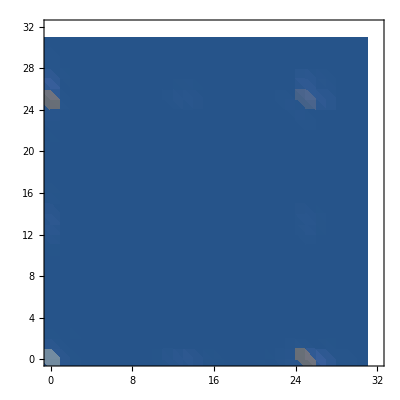

```mathematica
pstab = Table[RotateRight[pstab[[j]],Ny/2],{j,1,Length[pstab]}];
pstab = Transpose[pstab];
pstab =  Table[RotateRight[pstab[[j]],Nx/2],{j,1,Length[pstab]}];
pstab = Transpose[pstab];
dkx = 1.0;
dky = 1.0;
psdat = Table[{j dkx, k dky,pstab[[j+Nx/2+1,k + Ny/2+1]]},{j,-Nx/2,Nx/2-1},{k,-Ny/2,Ny/2-1}];
psdat = Partition[Flatten[psdat],3];
Gb = ListDensityPlot[psdat, PlotRange->{{0,32},{0,32},All}]
```

```mathematica
Gb = ListPlot3D[psdat, PlotRange->{{0,32},{0,32},All},ColorFunction->"GrayTones"]
```

-Graphics3D-

```mathematica
k1=ContourPlot[Sin[2Pi 10 x]Sin[2 Pi 10 y],{x,0,1},{y,0,1}]
```

-Graphics-

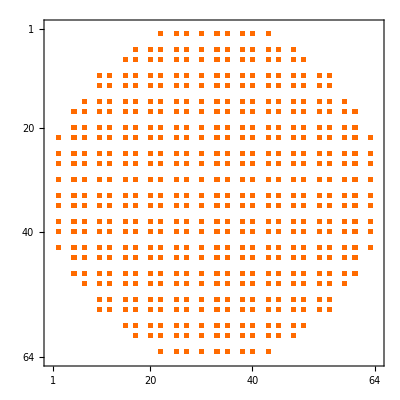

```mathematica
k2=MatrixPlot[Something]
```